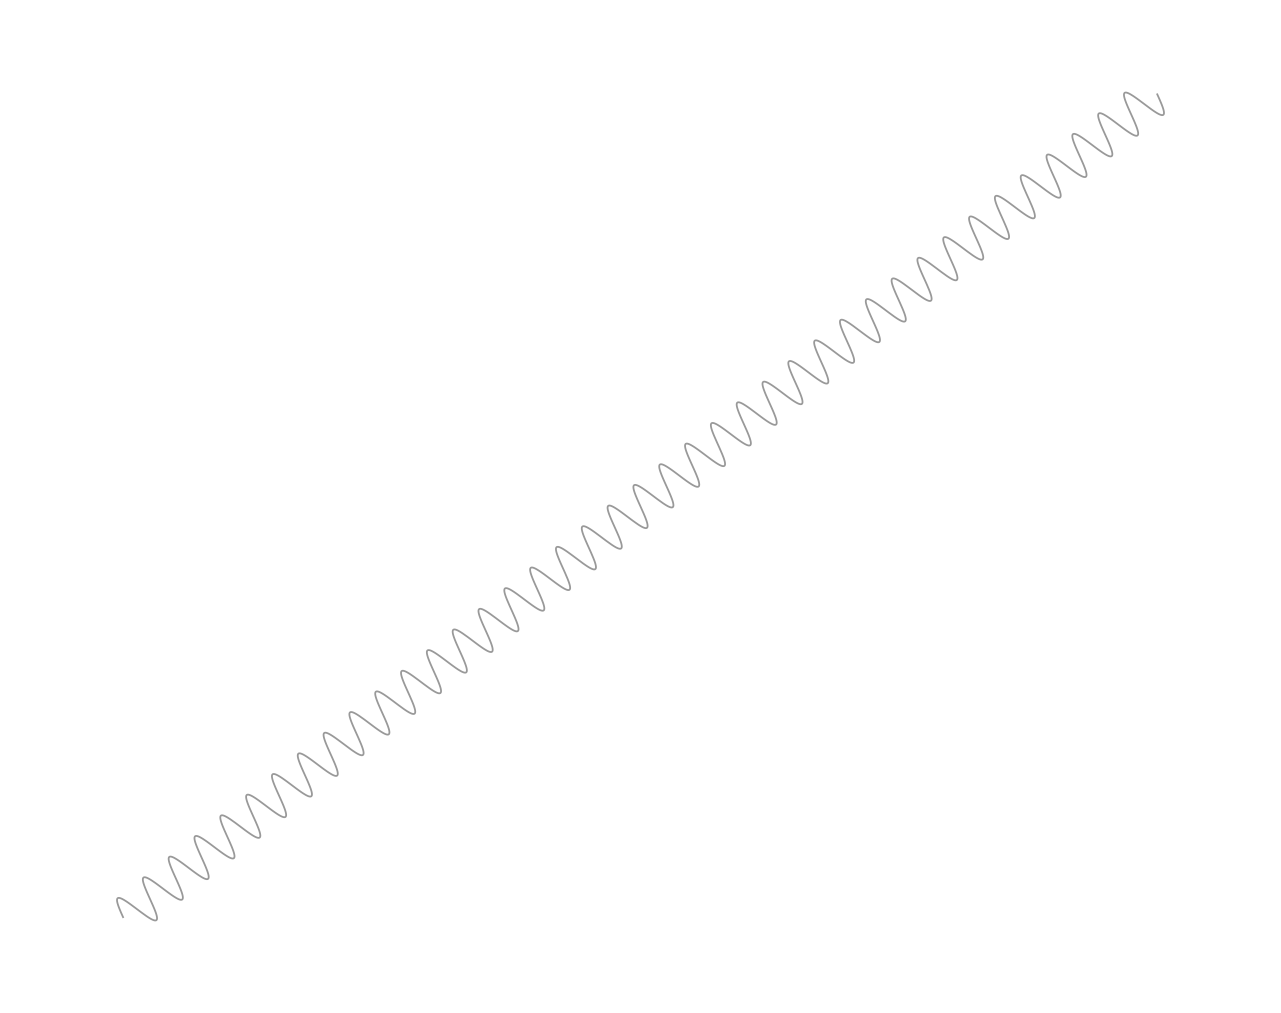

```mathematica
faktordebelina=.5;
SlikaVzmeti[r2_,ravna_,n_,R_,barva_]:=ParametricPlot[
RotationMatrix[{{1,0},r2}].Which[
u≤ravna,{u,0},
ravna<u<Norm[r2]-ravna,{u,R Sin[(2π n)/(Norm[r2]-2ravna)(u-ravna)]},
Norm[r2]-ravna≤u, {u,0}
],
{u,0,Norm[r2]},
Axes->False,
PlotStyle->Directive[RGBColor[barva],Thickness[faktordebelina*.002]]
];
r2={5,4};
ravna=0;
n=40;
R=.1;
barva=.6{1,1,1};
SlikaVzmeti[r2,ravna,n,R,barva]
```

```mathematica
velčrk=193.5;
faktordebelina=.5;
grafika=Show[


SlikaVzmeti[r2,ravna,n,R,barva],
Graphics[{
RGBColor[{1,0,0}],

Text[MaTeX["\\color{red}{\\mathbf{"<>ToString[If[#=={0,0},"r_1","r_2"]]<>"}}",FontSize->velčrk],#+{0,+.2}],

Disk[#,.02]
}]&/@{
{0,0},
r2
},

ΔV={-1,-3};
Graphics[{
Rotate[
Text[MaTeX["\\color{blue}{\\mathbf{V_2}-\\mathbf{V_1}}",FontSize->velčrk],(2r2+ΔV)/2+RotationMatrix[{{1,0},ΔV}].{0,.2}],
VectorAngle[{1,0},-ΔV]],
RGBColor[{0,0,1}],
Arrowheads[faktordebelina*.04],
Thickness[faktordebelina*.005],
Arrow[{r2,r2+ΔV}]
}],

Graphics[{
Rotate[
Text[MaTeX["\\color{red}{\\mathbf{r_1}-\\mathbf{r_2}}",FontSize->velčrk],r2/2+RotationMatrix[{{1,0},r2}].{0,.2}],
VectorAngle[{1,0},r2]],

RGBColor[{1,0,0}],
Arrowheads[faktordebelina*.04],
Thickness[faktordebelina*.005],
Arrow[{r2,{0,0}}]
}],

ImageSize->4*1920
];
Export["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png",grafika]
```

c:\Users\gal\Documents\ŠOLA\NAR\fiz\rn.aviončki\grafi\zavorna sila vzmeti.png

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```

```mathematica
SystemOpen["c:\\Users\\gal\\Documents\\ŠOLA\\NAR\\fiz\\rn.aviončki\\grafi\\zavorna sila vzmeti.png"]
```